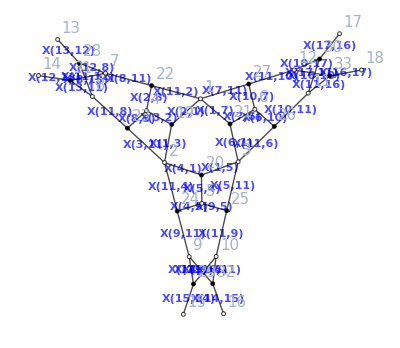

```mathematica
(*SPECIFY WHICH EXAMPLE IT IS*)
ii=33;

(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
topleft=a;
topright=b;
bottomleft=c;
bottomright=d;
viewGraph[a,b,c,d]
```

```mathematica
(*This is to fix my functional tests*)
```

```mathematica
reducibilityBFTQ[a,b,c,d,False,False,1]
reductionGraphBFT[a,b,c,d,1]

reducibilityBFTQ[a,b,c,d,False,False,2]
reductionGraphBFT[a,b,c,d,2]
```

False

{}

True

{{X[1,2]},{X[2,3]},{X[5,1]}}